Mohamed M. Hammad

Neural Network and Deep Learning with Mathematica                              < >    Ξ

Edited by Hao Feng

## 6 Learning Rate Schedules and Gradient Descent Variants

Remark:
This chapter provides a Mathematica implementation of the concepts and ideas presented in Chapter 5, [1], of the book titled Artificial Neural Network and Deep Learning: Fundamentals and Theory. We strongly recommend that you begin with the theoretical chapter to build a solid foundation before exploring the corresponding practical implementation.

In deep learning, the optimization process lies at the heart of training Neural Networks (NNs). Central to this optimization is the notion of the learning rate, a crucial hyperparameter that dictates the step size in the parameter space during optimization. Selecting an appropriate learning rate and its schedule significantly impacts the convergence speed and the final performance of the model. In this chapter, we delve into various learning rate schedules and adaptive algorithms that play pivotal roles in optimizing NNs. By understanding these techniques, practitioners can fine-tune their training processes and achieve better results in their machine-learning endeavors.

The chapter initiates an exploration of learning rate schedules [64-75], which entail predefined strategies for altering the learning rate throughout the training process. Learning rate schedules include step decay, inverse time decay, exponential decay, polynomial decay with warm restart, cyclical learning rate, stochastic gradient descent with warm restarts (cosine decay), exponential decay sine wave learning rate, Hessian-aware learning rate decay, etc., each with its own advantages and drawbacks. Understanding and appropriately implementing these schedules are crucial for achieving optimal convergence without encountering issues such as slow convergence or overshooting the minima.

Transitioning from learning rate schedules, we explore accelerated gradient descent [76-79], a variant of the traditional GD algorithm designed to speed up convergence. Two popular accelerated gradient descent algorithms are SGD with momentum and Nesterov accelerated gradient descent. In both cases, the momentum term helps the optimization algorithm to continue moving in the same direction or accelerate in the relevant direction, even if the gradient changes direction frequently or the surface of the loss function is highly irregular. Both methods help in smoothing out the updates, which is particularly useful when dealing with noisy or high-variance gradients common in SGD. The momentum term helps navigate through the irregularities of the loss surface more effectively, leading to a smoother and often faster path to the minimum. By leveraging past gradients, these methods can speed up convergence, reducing the time and computational resources needed for training. This leads to faster convergence and better overall performance in training NNs and other machine-learning models.

Following the discussion on accelerated gradient descent, we turn our attention to adaptive learning rate algorithms [80-93]. Adaptive learning rate algorithms adaptively adjust the learning rate during training based on past gradients, and other relevant metrics. These algorithms aim to strike a balance between the benefits of using large learning rates for fast convergence and the stability provided by smaller learning rates to prevent overshooting or oscillations. Popular examples include AdaGrad, RMSProp, AdaDelta, Adam, AdaMax, Nadam, and AMSGRAD, each with its own approach to adaptively scale the learning rates for individual model parameters.

Moreover, we explore second-order optimization methods [11,15,25,37]. Second-order optimization methods, such as Newton, Marquardt, and variants like conjugate gradient (Hestenes-Stiefel formula, Polak-Ribiere formula, Fletcher-Reeves formula), and quasi-Newton (rank one correction, DFP, and BFGS), etc., leverage information from the second derivatives of the loss function to guide the optimization process. By incorporating curvature information, these methods can converge faster and more accurately than first-order methods like GD. However, they often come with higher computational costs and memory requirements due to the need to compute and store second-order derivatives or their approximations.

This chapter serves as a continuation of the foundational principles introduced in Chapter 5. Here, we delve into the intricate landscape of learning rate schedules and adaptive algorithms, employing the computational power of Mathematica to elucidate their mechanisms and applications. Divided into two units, this chapter demystifies these fundamental concepts.

The first unit serves as a foundational exploration of learning rate schedules and adaptive optimization algorithms, leveraging the dynamic capabilities of Mathematica to provide intuitive insights. By building optimization algorithms from scratch, the reader gains a deeper understanding of the underlying principles. Through interactive manipulations, readers are guided step by step to comprehend the nuances of various algorithms. From elucidating traditional learning rate schedules such as step decay, inverse time decay, and exponential decay to unraveling sophisticated techniques like accelerated gradient descent and adaptive learning rate algorithms, this unit equips readers with a profound understanding of the mechanisms driving optimization processes. Moreover, Mathematica provides a comprehensive suite of built-in functions and tools for optimization, enabling users to implement, analyze, and visualize a diverse range of optimization problems.

In the second unit, the focus shifts towards practical applications, centering on the optimization of NNs using learning rate schedules and adaptive algorithms within the Mathematica environment. In this unit, we explore the powerful capabilities of Mathematica’s NetTrain function, leveraging a range of optimization methods and suboptions to fine-tune the training process and enhance model performance. NetTrain serves as the cornerstone of NN training within Mathematica, providing a versatile and user-friendly interface for optimizing model parameters. At the heart of NetTrain lies a suite of optimization methods, including “ADAM”, “RMSProp”, “SGD”, and “SignSGD”, each offering unique strategies for navigating the high-dimensional parameter space of NNs. We will not only explore the selection and utilization of these optimization methods but also, we will go into the intricacies of their associated suboptions. These suboptions, including “Momentum”, “Beta1”, “Beta2”, and “Epsilon”, provide users with fine- grained control over the optimization process, allowing for nuanced adjustments to suit the specific requirements of their NN architectures and training objectives.

Furthermore, the “LearningRateSchedule” suboption allows you to specify a learning rate schedule, which can be a fixed learning rate, a schedule that decreases the learning rate over time (such as exponential decay or step decay), or any other custom schedule you define. Through comprehensive demonstrations and hands-on exercises, this unit empowers practitioners to harness the full potential of learning rate schedules and adaptive algorithms in enhancing the performance of NNs.

Together, these units shed light on the nuanced interconnections among learning rate schedules, adaptive algorithms, and NN optimization.

### Understanding Learning Rate Schedules and Adaptive Algorithms with Mathematica

code 6.1 Step Decay

(* The code implements an interactive visualization tool using Mathematica’s Manipulate function to explore the behavior of a step decay learning rate schedule. Users can adjust two parameters, the drop factor (d) and step size (s), via sliders to observe their impact on the learning rate decay. The code defines a step decay function that computes the learning rate based on the initial learning rate, drop factor, step size, and current iteration. Data points representing the learning rate at each iteration are generated and plotted dynamically: *)

```mathematica
Manipulate[
Module[
{data},
stepDecay[initialLearningRate_,dropFactor_,stepSize_,currentIteration_]:=initialLearningRate*dropFactor^Floor[currentIteration/stepSize];

data=Table[{i,stepDecay[initialLearningRate,d,s,i]},{i,0,100}];

ListLinePlot[
data,
PlotRange->All,
PlotLabel->StringForm["Step Decay with d = `` and s = ``",d,s],
AxesLabel->{"Iterations","Learning Rate"},
ImageSize->300
]
],
{{d,0.5,"Drop Factor"},0.1,0.9,0.01},
{{s,10,"Step Size"},1,20,1},
Initialization:>{
initialLearningRate=0.2;
}
]
```

code 6.2 Inverse Time Decay

(* In this Manipulate interface, you can interactively choose different values for the decay rate and observe the corresponding learning rate decay plot. Adjust the decayRate slider to explore how the learning rate changes over iterations according to the inverse time decay formula: *)

```mathematica
Manipulate[
Module[
{data},

inverseTimeDecay[initialLearningRate_,decayRate_,currentIteration_]:=initialLearningRate/(1+decayRate*currentIteration);

data=Table[{i,inverseTimeDecay[initialLearningRate,d,i]},{i,0,100}];

ListLinePlot[
data,
PlotRange->{{0,100},{0.002,1}},
PlotLabel->StringForm["Inverse Time Decay \nInital Rate = `` \nd = ``",initialLearningRate,d],
AxesLabel->{"Iterations","Learning Rate"},
ImageSize->300
]
],
{{initialLearningRate,0.5,"Initial Learning Rate"},0.01,1,0.01},
{{d,0.5,"Decay Rate"},0.01,0.9,0.01}
]
```

code 6.3 Exponential Decay

(* The code uses the standard exponential decay formula, where the learning rate decreases exponentially with the increase in the step. Adjust the sliders for the initial learning rate and decay rate to observe how the learning rate changes over steps according to the standard exponential decay formula: *)

```mathematica
Manipulate[
Module[
{data},
exponentialDecay[initialLearningRate_,decayRate_,currentIteration_]:=initialLearningRate*Exp[-decayRate*currentIteration];

data=Table[{i,exponentialDecay[initialLearningRate,decayRate,i]},{i,0,100}];

ListLinePlot[
data,
PlotRange->{{0,100},{0.002,1}},
PlotLabel->StringForm["Exponetial Decay\nInitial Rate = ``,\nDecay Rate=``",initialLearningRate,decayRate],
AxesLabel->{"Iterations","Learning Rate"},
ImageSize->300
]
],
{{initialLearningRate,0.5,"Initial Learning Rate"},0.01,1,0.01},
{{decayRate,0.5,"Decay Rate"},0.1,1,0.01}
]
```

code 6.4 Exponential Decay and Inverse Time Decay

(* The code defines both exponential decay and inverse time decay functions and generates data for both methods. It then plots the learning rates over steps for comparison. Adjust the sliders for the initial learning rate, decay rate, and decay steps to observe how the learning rates evolve using both decay methods: *)

```mathematica
Manipulate[
Module[
{dataExp,dataInvTime},

exponentialDecay[initialLearningRate_,decayRate_,currentStep_]:=initialLearningRate*Exp[-decayRate*currentStep];
inverseTimeDecay[initialLearningRate_,decayRate_,currentIteration_]:=initialLearningRate/(1+decayRate*currentIteration);
dataExp=Table[{i,exponentialDecay[initialLearningRate,decayRate,i]},{i,0,100}];
dataInvTime=Table[{i,inverseTimeDecay[initialLearningRate,decayRate,i]},{i,0,100}];

ListLinePlot[
{dataExp,dataInvTime},
PlotRange->{{0,100},{0.002,1}},
PlotLabel->"Exponential Decay and Inverse Time Decay",
PlotLegends->Placed[{"Exponential Decay","Inverse Time Decay"},{0.7,0.78}],
AxesLabel->{"Iterations","Learning Rate"},
ImageSize->300
]
],
{{initialLearningRate,0.7,"Initial Learning Rate"},0.01,1,0.01},
{{decayRate,0.1,"Decay Rate"},0.01,0.9,0.001}
]
```

code 6.5 Polynomial Decay

(* The code aims to create an interactive visualization tool for exploring polynomial decay in learning rate dynamics. Utilizing Mathematica’s Manipulate function, users can dynamically adjust parameters such as the initial learning rate, power of the polynomial decay function, and total iterations via sliders. Within the module, a polynomial decay function is defined to compute the learning rate at each iteration based on the specified parameters. Data points representing the learning rate over iterations are generated and plotted using ListLinePlot, with the plot displaying the decay curve: *)

```mathematica
Manipulate[
Module[
{data},
polynomialDecay[initialLearningRate_,power_,totalIterations_,currentIteration_]:=initialLearningRate*(1-currentIteration/totalIterations)^power;

data=Table[{i,polynomialDecay[initialLearningRate,power,totalIterations,i]},{i,0,totalIterations}];

ListLinePlot[
data,
PlotRange->{{0,2000},{0.002,1}},
PlotLabel->StringForm["Polynomial Decay\nInitial Rate=``,Power=``,Total Iterations=``",initialLearningRate,power,totalIterations],
AxesLabel->{"Iterations","Learning Rate"},
ImageSize->300
]
],
{{initialLearningRate,0.7,"Initial Learning Rate"},0.01,1,0.01},
{{power,0.9,"Power"},0.1,2,0.1},
{{totalIterations,1500,"Total Iterations"},100,2000,100},
Initialization:>{(*Set parameters*)}
]
```

code 6.6 Polynomial Decay with Warm Restarts

(* The code aims to analyze and visualize polynomial decay with warm restarts, a technique often employed in training NN. It defines a function, polynomialDecayWithRestart, within a module to simulate learning rate decay with periodic resets to prevent convergence to suboptimal solutions. Parameters such as the initial learning rate, powers representing different decay rates, total iterations, and warm restart fractions are defined to allow for customizable exploration of decay strategies. Data lists are generated for various decay powers using nested table commands, and these are plotted using ListLinePlot. The resulting plot displays the learning rate strategies, with each curve representing a different decay rate: *)

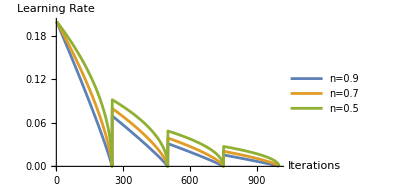

```mathematica
polynomialDecayWithRestart[initialLearningRate_,power_,totalEpochs_,restartFractions_,currentIterations_]:=Module[
{restartPoints,currentEpoch,currentLearningRate,currentIteration,totalEpoch},
restartPoints=Round[restartFractions*totalEpochs];

Piecewise[
{
{{currentLearningRate,totalEpoch}={initialLearningRate,restartPoints[[1]]};,
restartPoints[[1]]>=currentIterations>=1},
{{currentLearningRate,totalEpoch}={initialLearningRate*0.65,restartPoints[[2]]};,
restartPoints[[2]]>=currentIterations>=restartPoints[[1]]+1},
{{currentLearningRate,totalEpoch}={initialLearningRate*0.65^2,restartPoints[[3]]};,
restartPoints[[3]]>=currentIterations>=restartPoints[[2]]+1},
{{currentLearningRate,totalEpoch}={initialLearningRate*0.65^3,totalEpochs};,
totalEpochs>=currentIterations>=restartPoints[[3]]+1}
}
];
currentLearningRate*(1-currentIterations/totalEpoch)^power
];

initialLearningRate=0.2;
powers={0.9,0.7,0.5};
totalIterations=1000;
restartFractions={0.25,0.5,0.75};

dataLists=Table[
Table[
{i,polynomialDecayWithRestart[initialLearningRate,power,totalIterations,restartFractions,i]},
{i,0,totalIterations}
],
{power,powers}
];

ListLinePlot[
dataLists,
PlotRange->All,
AxesLabel->{"Iterations","Learning Rate"},
PlotLegends->Placed[{"n=0.9","n=0.7","n=0.5"},{0.85,0.78}],
ImageSize->300
]
```

code 6.7 Cyclical Learning Rates

(* Cyclical Learning Rates (CLR) proves particularly valuable in overcoming challenges associated with saddle points in the loss landscape. The code presented below creates an interactive environment for exploring the impact of different parameters on the cyclical learning rate schedule. Key Parameters adjusted via Manipulate are base learning rate, the initial learning rate at the start of each cycle, max learning rate, the peak learning rate reached during a cycle, half cycle length, a parameter controlling how quickly the learning rate increases and decreases, and total iterations, the number of iterations to visualize. As users manipulate these parameters using sliders, the code dynamically recalculates and visualizes the corresponding cyclical learning rate schedule. The resulting plot provides insights into how changes in the learning rate parameters impact the training process, offering an intuitive understanding of CLR’s adaptability and efficiency: *)

```mathematica
triangularLR[epoch_,stepsize_,baseLR_,maxLR_]:=Module[
{cycle,x,lr},
cycle=Floor[1+epoch/(2*stepsize)];
x=Abs[epoch/stepsize-2*cycle+1];
lr=baseLR+(maxLR-baseLR)*Max[0,(1-x)];
lr 
]

Manipulate[
Module[
{epochs,LearningRates},
epochs=Range[1,totalIterations];
LearningRates=triangularLR[#,stepsize,baseLR,maxLR]&/@epochs;

ListLinePlot[
Transpose[{epochs,LearningRates}],
PlotLabel->"Cyclical Learning Rate Schedule",
PlotRange->{{1,200},{0.005,0.4}},
Joined->True,
Mesh->All,
MeshStyle->Directive[PointSize[0.01],Purple],
ImageSize->300
]
],
{{baseLR,0.1,"Base Learning Rate"},0.1,0.2,0.0001,Appearance->"Labeled"},{{maxLR,0.2,"Max Learning Rate"},0.2,0.3,0.001,Appearance->"Labeled"},{{stepsize,5,"Half Cycle Length"},5,10,1,Appearance->"Labeled"},{{totalIterations,100,"Total Epochs"},10,200,20,Appearance->"Labeled"}
]
```

code 6.8 Cosine Annealing Learning Rate Scheduler

(* The code implements a cosine annealing learning rate scheduler within a Manipulate environment, allowing users to interactively explore and visualize the learning rate schedule. It defines a function, CosineAnnealingLR, to compute learning rates based on parameters such as the minimum and maximum learning rates, total iterations in a cycle, and the current iteration number. The code generates learning rates over multiple cycles using the cosine annealing method and plots the learning rate schedule using ListLinePlot. Users can adjust hyperparameters such as the minimum and maximum learning rates, total iterations in a cycle, and the number of cycles through sliders to observe the corresponding changes in the learning rate schedule: *)

```mathematica
Manipulate[
CosineAnnealingLR[minLR,maxLR,Ti,Tcur_]:=minLR+0.5(maxLR-minLR)(1+Cos[(Tcur/Ti)π]);
cycles=Flatten[Table[Range[0,Ti],numCycles]];
learningRates=CosineAnnealingLR[minLR,maxLR,Ti,#]&/@cycles;
epochs=Range[1,Length[cycles]];
data=Transpose[{epochs,learningRates}];

ListLinePlot[
data,
PlotRange->{{1,1000},{0.005,0.15}},
AxesLabel->{"Iterations","Learning Rate"},
PlotLabel->"Cosine Annealing Learning Rate Schedule",
Joined->True,
ImageSize->300
],
{{minLR,0.02,"Minimum LR"},0,0.1,0.0001,Appearance->"Labeled"},{{maxLR,0.08,"Maximum LR"},0,0.1,0.0001,Appearance->"Labeled"},{{Ti,50,"Total Iterations in a Cycle"},10,100,1,Appearance->"Labeled"},{{numCycles,4,"Total Cycles"},1,10,1,Appearance->"Labeled"}
]
```

code 6.9 Stochastic Gradient Descent with Restarts

(* The code constructs a learning rate schedule based on the stochastic gradient descent with restarts (SGDR) method utilizing cosine annealing. It initializes parameters such as the multiplier factor for cycle length, the initial cycle length, and the number of cycles. Subsequently, it calculates the cycle lengths and computes learning rates for each iteration within each cycle using the SGDRCosineLR function, which implements the cosine annealing formula. The resulting learning rate schedule is then visualized using ListLinePlot, displaying epochs against corresponding learning rates: *)

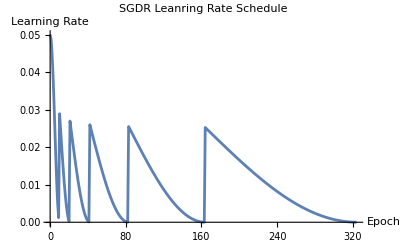

```mathematica
Tmult=2;
T[0]=10;
numofcycles=4;

Ti=Table[T[i+1]=T[i]*Tmult;T[i+1],{i,0,numofcycles}];
TiValues=Flatten[PrependTo[Ti,{1,T[0]}]];

nmin=0.0;
nmax=0.05;
SGDRCosineLR[nmin_,nmax_,Tcur_,Ti_]:=nmin+1/2(nmax-nmin)(1+Cos[Tcur/Ti π])

lrValues=Flatten[Table[
Table[
SGDRCosineLR[nmin,nmax,t,TiValues[[j+1]]],
{t,TiValues[[j]]-1,TiValues[[j+1]]-1}
],
{j,1,Length[TiValues]-1}
]];

epochs=Range[0,Length[lrValues]-1];

ListLinePlot[
Transpose[{epochs,lrValues}],
AxesLabel->{"Epoch","Learning Rate"},
PlotLabel->"SGDR Leanring Rate Schedule"
]
```

code 6.10 Exponential Decay Sine Wave Learning Rate

(* The code implements a Manipulate interface in Mathematica, facilitating interactive exploration of a custom learning rate schedule. The schedule is defined by a function combining exponential decay and sine wave oscillation components. Users can adjust parameters such as the initial learning rate, decay rate, total iterations, oscillation parameter, and number of batches per epoch. These parameters influence the shape and behavior of the learning rate schedule, impacting the optimization process. The interface dynamically updates a plot showcasing the learning rate schedule, enabling users to visualize how changes in parameters affect the rate at which the algorithm adjusts its weights during training: *

```mathematica
Manipulate[
Module[
{lrFunction,initialRate,decayRate,totalIterations,oscillationParam,batchesPerEpoch},
lrFunction[t_,initialRate_,decayRate_,totalIterations_,oscillationParam_,batchesPerEpoch_]:=initialRate Exp[-(decayRate t)/totalIterations](Sin[(oscillationParam t)/(2π batchesPerEpoch)]+Exp[-(decayRate t)/totalIterations]+0.5);

initialRate=initialRate0;
decayRate=decayRate0;
totalIterations=totalIterations0;
oscillationParam=oscillationParam0;
batchesPerEpoch=batchesPerEpoch0;

Plot[
lrFunction[t,initialRate,decayRate,totalIterations,oscillationParam,batchesPerEpoch],
{t,0,totalIterations},
AxesLabel->{"Iteration","Learning Rate"},
PlotRange->{Automatic,{0.005,2.5}},
ImageSize->300
]
],
{{initialRate0,0.59,"Initial learning rate (α₀)"},0,1,0.01},{{decayRate0,0.6,"Decay rate (ρ)"},0,1,0.01},{{totalIterations0,50000,"Total iterations (T)"},100,1000000,1000},{{oscillationParam0,0.05,"Oscillation parameter (τ)"},0,1,0.01},{{batchesPerEpoch0,10,"Number of batches per epoch (b)"},1,100,1},ControlPlacement->Left
]
```

code 6.11 Hessian-Aware Learning Rate Schedule

(* The code creates a Manipulate interface that allows users to visualize and interact with the Hessian-Aware Learning Rate schedule based on specific parameters. The code defines a piecewise learning rate function, allowing for different learning rates to be applied in various epochs of the training process. Users can adjust parameters such as the initial learning rate, decay factor, starting epoch for decay, ending epoch for decay, and total number of epochs. The interface dynamically updates the plotted learning rate decay curve based on the chosen parameter values, providing users with insights into how changes in these parameters affect the learning rate schedule during training: *)

```mathematica
Manipulate[
Module[
{lr,decayFunc,data},
decayFunc[t_]:=decayFunc[t-1]*decayFactor^(1/(endEpoch-startEpoch));
lr[t_,initialLR_,decayFactor_,startEpoch_,endEpoch_,totalEpochs_]:=Piecewise[
{
{initialLR,1<=t<startEpoch},
{decayFunc[t],startEpoch<t<=endEpoch},
{decayFactor*initialLR,endEpoch<t<=totalEpochs}
}
];

decayFunc[startEpoch]=initialLR;

data=Table[{t,lr[t,initialLR,decayFactor,startEpoch,endEpoch,totalEpochs]},{t,1,totalEpochs}];
ListLinePlot[
data,
PlotRange->{{1,1000},{0,1}},
AxesLabel->{"Epoch","Learning Rate"},
PlotRange->All,
GridLines->{{startEpoch,endEpoch},{initialLR,decayFactor*initialLR}},
Epilog->{
Text["initialLR",{startEpoch,initialLR},{3,2}],
Text["decayFactor*initialLR",{endEpoch,decayFactor*initialLR},{-1,-1}]
}
]
],
{{initialLR,0.7,"Initial learning rate (initialLR)"},0,1,0.01},{{decayFactor,0.28,"Decay factor (decayFactor)"},0,1,0.01},{{startEpoch,350,"Starting epoch for decay (startEpoch)"},1,totalEpochs-1,1},{{endEpoch,480,"Ending epoch for decay (endEpoch)"},startEpoch+1,totalEpochs,1},{{totalEpochs,900,"Total number of epochs (totalEpochs)"},10,1000,10},ControlPlacement->Left
]
```

code 6.12 Gradient Descent with Momentum (1D)

(* The code showcases the implementation and visualization of gradient descent with momentum for optimizing the function f(x)=x^2*sin(x). The code defines the function and its derivative, then employs a gradient descent algorithm with momentum to iteratively update the value of x towards the minimum of the function. Through interactive controls, users can adjust parameters such as the initial point, number of steps, learning rate, and momentum parameter, allowing them to observe how different settings affect the optimization process, convergence speed, and trajectory: *)

```mathematica
targetFunction[x_]:=x^2*Sin[x]

functionDerivative[x_]:=x^2 Cos[x]+2 x Sin[x]

gradientDescentWithMomentum[func_,funcDerivative_,initialPoint_,learningRate_,momentumParameter_,iterations_]:=Module[
{x=initialPoint,v=0,path={initialPoint}},
For[
i=1,
i<=iterations,
i++,

v=momentumParameter*v-learningRate*funcDerivative[x];
x=x+v;
AppendTo[path,x];
];
Return[path];
]

Manipulate[
path=gradientDescentWithMomentum[targetFunction,functionDerivative,initialPoint,learningRate,momentumParameter,steps];

Plot[
targetFunction[x],
{x,-5,9},
Epilog->{Purple,PointSize[0.02],Point[Thread[{path,targetFunction/@path}]]},
PlotLabel->"Gradient Descent with Momentum",
AxesLabel->{"x","f(x)"},
ImageSize->300
],
{{initialPoint,-5,"Initial Point"},-6,6,Appearance->"Labeled"},{{steps,1,"Steps"},1,50,1,Appearance->"Labeled"},{{learningRate,0.01,"Learning Rate"},0.001,0.1,Appearance->"Labeled"},{{momentumParameter,0.95,"Momentum Parameter"},0.1,0.99,Appearance->"Labeled"}
]
```

code 6.13 Gradient Descent with Momentum (2D)

(* The code defines a target function f(x,y)=x^2*sin(x)+y^2*sin(y) and its gradient, and implements gradient descent with momentum for optimization. It allows interactive manipulation of parameters such as the initial point, number of iterations, learning rate, and momentum parameter. The optimization process is visualized through a contour plot of the target function overlaid with the optimization path and step direction arrows. The primary goal is to demonstrate the convergence of the gradient descent algorithm with momentum towards the minimum point of the target function, providing an intuitive understanding of the optimization process: *)

```mathematica
targetFunction[x_,y_]=x^2*Sin[x]+y^2*Sin[y];
functionGradient[x_,y_]=Grad[targetFunction[x,y],{x,y}];

gradientDescentWithMomentum[func_,grad_,initialPoint_,learningRate_,momentumParameter_,iterations_]:=Module[
{x=initialPoint,v={0,0},path={initialPoint}},
For[
i=1,
i<=iterations,
i++,

v=momentumParameter*v-learningRate*grad@@x;
x=x+v;
AppendTo[path,x];
];
Return[path];
];

Manipulate[
Module[
{path,minPoint},
path=gradientDescentWithMomentum[targetFunction,functionGradient,initialPoint,learningRate,momentumParameter,iterations];
stepArrows=Arrow/@Partition[path,2,1];

Show[
ContourPlot[
targetFunction[x,y],
{x,-10,10},
{y,-10,10},
Contours->10,
ContourStyle->{White},
ClippingStyle->Automatic,
ColorFunction->"BlueGreenYellow",
ImageSize->300,
PlotLegends->Automatic,
PlotLabel->"Gradient Descent with Momentum",
AspectRatio->Automatic
],
Graphics[
{
Blue,
PointSize[0.015],
Point[path],
Purple,
stepArrows
}
]
]
],
{{initialPoint,{-5.3,7.6},"Initial Point"},{-10,-10},{10,10},Appearance->"Labeled"},{{iterations,1,"Iterations"},1,100,1,Appearance->"Labeled"},{{learningRate,0.001,"Learning Rate"},0.001,0.01,Appearance->"Labeled"},{{momentumParameter,0.99,"Momentum Parameter"},0.1,0.99,Appearance->"Labeled"},TrackedSymbols:>{initialPoint,iterations,learningRate,momentumParameter}
]
```

code 6.14 Nesterov Accelerated Gradient Descent

(* The code implements an interactive visualization of the Nesterov Accelerated Gradient Descent optimization algorithm. It defines an objective function f(x1,x2)=sin(x1)+cos(x2) and its gradient, allowing users to adjust parameters such as learning rate, momentum, number of iterations, and initial guess through interactive controls. Within a module, the Nesterov Accelerated Gradient Descent algorithm is executed, updating parameters iteratively and storing the trajectory of parameter updates. The visualization consists of a contour plot of the objective function overlaid with the trajectory of parameter updates, enabling users to observe how the optimization algorithm progresses towards the function’s minimum, with arrows indicating the direction of parameter updates at each iteration: *)

```mathematica
Manipulate[
Module[
{f,gradient,learningRate,momentum,numIterations,initialGuess,x,v,trajectory},
f[x1_,x2_]=Sin[x1]+Cos[x2];
gradient[x1_,x2_]={D[f[x1,x2],x1],D[f[x1,x2],x2]};

learningRate=lr;
momentum=m;
numIterations=n;
initialGuess={x0,y0};

x=initialGuess;
v={0,0};
trajectory={x};

Do[
lookaheadParams=x+momentum*v;
grad=gradient@@lookaheadParams;

v=momentum*v-learningRate*grad;
x=x+v;
AppendTo[trajectory,x],
{i,numIterations}
];
{
Plot3D[
f[x1,x2],
{x1,-5,5},
{x2,-5,5},
PlotRange->All,
Mesh->None,
ImageSize->300,
ColorFunction->"BlueGreenYellow",
PlotLabel->"Nesterov Accelerated Gradient Descent Trajectory"],
ContourPlot[
f[x1,x2],
{x1,-5,5},
{x2,-5,5},
PlotRange->All,
Contours->10,
ContourStyle->{White},
ClippingStyle->Automatic,
ColorFunction->"BlueGreenYellow",
ImageSize->300,
PlotLegends->Automatic,
Epilog->{
Red,
PointSize[Medium],
Point[trajectory],
Blue,
Arrowheads[0.02],
Table[
Arrow[{trajectory[[i]],trajectory[[i+1]]}],
{i,Length[trajectory]-1}
]
},
FrameLabel->{"x1","x2"},
PlotLabel->"Nesterov Accelerated Gradient Descent Trajectory"
]
}
],
{{lr,0.1,"Learning Rate"},0.01,1,0.01},{{m,0.9,"Momentum"},0,1,0.01},{{n,1,"Number of Iterations"},1,50,1},{{x0,1.5,"Initial x1"},-4,4,0.1},{{y0,-0.5,"Initial x2"},-4,4,0.1}
]
```

code 6.15 AdaGrad Optimization

(* The code implements AdaGrad optimization to optimize the objective function sin(x)+cos(y). It defines functions to compute the gradient of the objective function, as well as the AdaGrad optimization procedure itself. Through a Manipulate interface, users can interactively set initial variable values, learning rate, epsilon, and the maximum number of iterations, while visualizing the trajectory of the optimization process on a contour plot of the objective function: *)

```mathematica
objectiveFunction[x_,y_]=Sin[x]+Cos[y];
gradientObjectiveFunction[x_,y_]={D[objectiveFunction[x,y],x],D[objectiveFunction[x,y],y]};

AdaGradOptimization[gradient_,learningRate_,epsilon_,variables_,accumulatedGradients_]:=Module[
{updatedVariables,updatedAccumulatedGradients},
updatedAccumulatedGradients=MapThread[#1+#2^2&,{accumulatedGradients,gradient}];
updatedVariables=MapThread[#1-(learningRate/Sqrt[#2+epsilon])#3&,{variables,updatedAccumulatedGradients,gradient}];
{updatedVariables,updatedAccumulatedGradients}
];

OptimizeWithAdaGrad[initialVariables_,learningRate_,epsilon_,maxIterations_]:=Module[
{variables,accumulatedGradients,trajectory},
variables=initialVariables;
accumulatedGradients=ConstantArray[0,Length[initialVariables]];
trajectory={variables};
Do[
grad=gradientObjectiveFunction@@variables;
{variables,accumulatedGradients}=AdaGradOptimization[grad,learningRate,epsilon,variables,accumulatedGradients];
AppendTo[trajectory,variables];,
{i,maxIterations}
];
trajectory
];

Manipulate[
initialVariables={initialX,initialY};
trajectory=OptimizeWithAdaGrad[initialVariables,learningRate,epsilon,maxIterations];
Show[
ContourPlot[
objectiveFunction[x,y],
{x,-5,5},
{y,-5,5},
PlotLegends->Automatic,
PlotLabel->"Trajectory of AdaGrad Optimization",
Contours->10,
ContourStyle->{White},
ClippingStyle->Automatic,
ColorFunction->"BlueGreenYellow",
ImageSize->300
],
Graphics[
{Purple,Arrowheads[Small],Arrow/@Partition[trajectory,2,1]}
]
],
{{initialX,2,"Initial X"},-5,5,Appearance->"Labeled"},{{initialY,1,"Initial Y"},-5,5,Appearance->"Labeled"},{{learningRate,0.4,"Learning Rate"},0.01,1,0.01,Appearance->"Labeled"},{{epsilon,10^(-6),"Epsilon"},10^(-8),10^(-4),10^(-8),Appearance->"Labeled"},{{maxIterations,1,"Max Iterations"},1,30,1,Appearance->"Labeled"}
]
```

code 6.16 RMSProp Optimization

(* The code implements RMSProp optimization to minimize the objective function sin(x)+cos(y). It defines the objective function and its gradient, implements the RMSProp optimization algorithm to iteratively update parameters based on gradients, and visualizes the optimization process using Manipulate. Users can adjust parameters such as initial values, learning rate, decay rate, epsilon, and maximum iterations to observe the trajectory of optimization on a contour plot of the objective function. This interactive visualization allows for an intuitive understanding of how different parameters affect the optimization process, facilitating experimentation and tuning for optimal performance: *)

```mathematica
objectiveFunction[x_,y_]=Sin[x]+Cos[y];
gradientObjectiveFunction[x_,y_]={D[objectiveFunction[x,y],x],D[objectiveFunction[x,y],y]};

RMSProp[grad_,lr_,decayRate_,epsilon_,vars_,varsSquaredGradients_]:=Module[
{updatedVars,updatedVarsSquaredGradients},
updatedVarsSquaredGradients=decayRate*varsSquaredGradients+(1-decayRate)*grad^2;
updatedVars=vars-(lr/Sqrt[updatedVarsSquaredGradients+epsilon])grad;
{updatedVars,updatedVarsSquaredGradients}
];

OptimizeRMSProp[initialVars_,lr_,decayRate_,epsilon_,maxIterations_]:=Module[
{vars,varsSquaredGradients,trajectory},
vars=initialVars;
varsSquaredGradients=ConstantArray[0,Length[initialVars]];
trajectory={vars};
Do[
grad=gradientObjectiveFunction@@vars;
{vars,varsSquaredGradients}=RMSProp[grad,lr,decayRate,epsilon,vars,varsSquaredGradients];
AppendTo[trajectory,vars];,
{i,maxIterations}
];
trajectory];

Manipulate[
initialVars={initialX,initialY};
trajectory=OptimizeRMSProp[initialVars,lr,decayRate,epsilon,maxIterations];

Show[
ContourPlot[
objectiveFunction[x,y],
{x,-5,5},
{y,-5,5},
PlotLegends->Automatic,
PlotLabel->"Trajectory of RMSProp Optimization",
Contours->10,
ContourStyle->{White},
ClippingStyle->Automatic,
ColorFunction->"BlueGreenYellow",
ImageSize->300
],
Graphics[
{Purple,Arrowheads[Small],Arrow/@Partition[trajectory,2,1]}
]
],
{{initialX,2,"Initial X"},-5,5,Appearance->"Labeled"},{{initialY,1,"Initial Y"},-5,5,Appearance->"Labeled"},{{lr,0.1,"Learning Rate"},0.01,1,0.01,Appearance->"Labeled"},{{decayRate,0.9,"Decay Rate"},0.1,0.99,0.01,Appearance->"Labeled"},{{epsilon,10^(-6),"Epsilon"},10^(-8),10^(-4),10^(-8),Appearance->"Labeled"},{{maxIterations,1,"Max Iterations"},1,100,1,Appearance->"Labeled"}
]
```

code 6.17 AdaDelta Optimization

(* The code aims to optimize the objective function sin(x)+cos(y) using the AdaDelta optimization algorithm. It begins by defining the objective function and its gradient, followed by the implementation of the AdaDelta optimization method, which iteratively updates parameters based on gradients and accumulations. Through the manipulation interface, users can adjust initial values, the decay rate (ρ), epsilon, and maximum iterations to observe the trajectory of optimization on a contour plot of the objective function. The interactive visualization aids in understanding the behavior of the optimization algorithm under different parameter settings, offering insights into its convergence process: *)

```mathematica
objectiveFunction[x_,y_]=Sin[x]+Cos[y];
gradientObjectiveFunction[x_,y_]={D[objectiveFunction[x,y],x],D[objectiveFunction[x,y],y]};

AdaDelta[grad_,rho_,epsilon_,vars_,accumulators_,deltas_]:=Module[
{updatedVars,updatedAccumulators,updatedDeltas,dx},
updatedAccumulators=rho*accumulators+(1-rho)*grad^2;
dx=(Sqrt[deltas+epsilon]/Sqrt[updatedAccumulators+epsilon])*grad;
updatedDeltas=rho*deltas+(1-rho)*dx^2;

updatedVars=vars-dx;
{updatedVars,updatedAccumulators,updatedDeltas}
];

OptimizeAdaDelta[initialVars_,rho_,epsilon_,maxIterations_]:=Module[
{vars,accumulators,deltas,trajectory},
vars=initialVars;
accumulators=ConstantArray[0,Length[initialVars]];
deltas=ConstantArray[0,Length[initialVars]];
trajectory={vars};

Do[
grad=gradientObjectiveFunction@@vars;
{vars,accumulators,deltas}=AdaDelta[grad,rho,epsilon,vars,accumulators,deltas];
AppendTo[trajectory,vars];,
{i,maxIterations}
];
trajectory];

Manipulate[
initialVars={initialX,initialY};
trajectory=OptimizeAdaDelta[initialVars,rho,epsilon,maxIterations];
Show[
ContourPlot[
objectiveFunction[x,y],
{x,-6,6},
{y,-6,6},
PlotLegends->Automatic,
PlotLabel->"Trajectory of AdaDelta Optimization",
Contours->10,
ContourStyle->{White},
ClippingStyle->Automatic,
ColorFunction->"BlueGreenYellow",
ImageSize->300
],
Graphics[
{Purple,Arrowheads[Small],Arrow/@Partition[trajectory,2,1]}
]
],
{{initialX,2,"Initial X"},-5,5,Appearance->"Labeled"},{{initialY,1,"Initial Y"},-5,5,Appearance->"Labeled"},{{rho,0.9,"Rho"},0.1,0.99,0.01,Appearance->"Labeled"},{{epsilon,10^(-6),"Epsilon"},10^(-8),10^(-4),10^(-8),Appearance->"Labeled"},{{maxIterations,1,"Max Iterations"},1,600,1,Appearance->"Labeled"}
]
```

code 6.18 Adam Optimization

(* The code aims to minimize the objective function sin(x)+cos(y) using the Adam optimization algorithm. It begins by defining the objective function and its gradient. The Adam algorithm is then implemented, updating parameters iteratively based on gradients and moving averages of past gradients and squared gradients. Through an interactive visualization using Manipulate, users can adjust parameters such as initial values, learning rate, beta1, beta2, epsilon, and maximum iterations to observe the trajectory of optimization on a contour plot of the objective function. This visualization facilitates an intuitive understanding of how different parameters influence the optimization process and aids in tuning for optimal performance: *)

```mathematica
objectiveFunction[x_,y_]=Sin[x]+Cos[y];
gradientObjectiveFunction[x_,y_]={D[objectiveFunction[x,y],x],D[objectiveFunction[x,y],y]};

Adam[grad_,lr_,beta1_,beta2_,epsilon_,vars_,m_,v_,t_]:=Module[
{mnew,vnew,mhat,vhat,varsnew},
mnew=beta1*m+(1-beta1)*grad;
vnew=beta2*v+(1-beta2)*grad^2;
mhat=mnew/(1-beta1^t);
vhat=vnew/(1-beta2^t);
varsnew=vars-(lr/Sqrt[vhat+epsilon])mhat;
{varsnew,mnew,vnew}
];

OptimizeAdam[initialVars_,lr_,beta1_,beta2_,epsilon_,maxIterations_]:=Module[
{vars,m,v,t,trajectory},
vars=initialVars;
m=ConstantArray[0,Length[initialVars]];
v=ConstantArray[0,Length[initialVars]];
t=0;
trajectory={vars};

Do[
grad=gradientObjectiveFunction@@vars;
t++;
{vars,m,v}=Adam[grad,lr,beta1,beta2,epsilon,vars,m,v,t];
AppendTo[trajectory,vars];,
{i,maxIterations}
];
trajectory];

Manipulate[
initialVars={initialX,initialY};
trajectory=OptimizeAdam[initialVars,lr,beta1,beta2,epsilon,maxIterations];

Show[
ContourPlot[
objectiveFunction[x,y],
{x,-5,5},
{y,-5,5},
PlotLegends->Automatic,
PlotLabel->"Trajectory of Adam Optimization",
Contours->10,
ContourStyle->{White},
ClippingStyle->Automatic,ColorFunction->"BlueGreenYellow",
ImageSize->300
],
Graphics[(*Plot arrows to indicate the direction of movement:*){Purple,Arrowheads[Small],Arrow/@Partition[trajectory,2,1]}]],(*Controls for Manipulate:*){{initialX,2,"Initial X"},-5,5,Appearance->"Labeled"},{{initialY,1,"Initial Y"},-5,5,Appearance->"Labeled"},{{lr,0.1,"Learning Rate"},0.001,0.2,0.001,Appearance->"Labeled"},{{beta1,0.9,"Beta1"},0,1,0.01,Appearance->"Labeled"},{{beta2,0.999,"Beta2"},0,1,0.001,Appearance->"Labeled"},{{epsilon,10^(-8),"Epsilon"},10^(-10),10^(-6),10^(-10),Appearance->"Labeled"},{{maxIterations,1,"Max Iterations"},1,100,1,Appearance->"Labeled"} ]
```

code 6.19 AdaMax Optimization

(* The code aims to optimize the objective function sin(x)+cos(y) using the AdaMax optimization algorithm. It begins by defining the objective function and its gradient, essential for the optimization process. The AdaMax algorithm, characterized by its unique update rules for moving averages of gradients, is then implemented to iteratively update parameters such as learning rate, beta1, beta2, and epsilon to minimize the objective function. Through an interactive visualization using Manipulate, users can adjust parameters and observe the trajectory of optimization on a contour plot of the objective function, providing insights into the optimization process and facilitating parameter tuning for optimal performance: *)

```mathematica
objectiveFunction[x_,y_]=Sin[x]+Cos[y];
gradientObjectiveFunction[x_,y_]={D[objectiveFunction[x,y],x],D[objectiveFunction[x,y],y]};

AdaMax[grad_,lr_,beta1_,beta2_,epsilon_,vars_,m_,u_,t_]:=Module[
{mnew,unew,varsnew},
mnew=beta1*m+(1-beta1)*grad;
unew=Max[beta2*u,Abs[grad]];
varsnew=vars-(lr/(1-beta1^t))*(mnew/unew);
{varsnew,mnew,unew}];

OptimizeAdaMax[initialVars_,lr_,beta1_,beta2_,epsilon_,maxIterations_]:=Module[
{vars,m,u,t,trajectory},
vars=initialVars;
m=ConstantArray[0,Length[initialVars]];
u=ConstantArray[0,Length[initialVars]];
t=0;
trajectory={vars};

Do[
grad=gradientObjectiveFunction@@vars;
t++;
{vars,m,u}=AdaMax[grad,lr,beta1,beta2,epsilon,vars,m,u,t];
AppendTo[trajectory,vars];,
{i,maxIterations}
];
trajectory];

Manipulate[initialVars={initialX,initialY};
trajectory=OptimizeAdaMax[initialVars,lr,beta1,beta2,epsilon,maxIterations];
Show[ContourPlot[objectiveFunction[x,y],{x,-5,5},{y,-5,5},PlotLegends->Automatic,PlotLabel->"Trajectory of AdaMax Optimization",Contours->10,ContourStyle->{White},ClippingStyle->Automatic,ColorFunction->"BlueGreenYellow",ImageSize->300],Graphics[{Purple,Arrowheads[Small],Arrow/@Partition[trajectory,2,1]}]],{{initialX,2,"Initial X"},-5,5,Appearance->"Labeled"},{{initialY,1,"Initial Y"},-5,5,Appearance->"Labeled"},{{lr,0.1,"Learning Rate"},0.001,0.2,0.001,Appearance->"Labeled"},{{beta1,0.9,"Beta1"},0,1,0.01,Appearance->"Labeled"},{{beta2,0.999,"Beta2"},0,1,0.001,Appearance->"Labeled"},{{epsilon,10^(-8),"Epsilon"},10^(-10),10^(-6),10^(-10),Appearance->"Labeled"},{{maxIterations,1,"Max Iterations"},1,100,1,Appearance->"Labeled"} ]
```

code 6.20 AMSGrad Optimization

(* The code aims to optimize the objective function sin(x)+cos(y) using the AMSGrad optimization algorithm, which addresses limitations of other algorithms like Adam by maintaining a maximum of past squared gradients. It begins by defining the objective function and its gradient, essential components for the optimization process. The AMSGrad algorithm is then implemented to iteratively update parameters such as learning rate, beta1, beta2, and epsilon, with the goal of minimizing the objective function. Through an interactive visualization using Manipulate, users can explore the trajectory of optimization on a contour plot of the objective function, gaining insights into the optimization process and the impact of different parameter settings on convergence behavior: *)

```mathematica
objectiveFunction[x_,y_]=Sin[x]+Cos[y];
gradientObjectiveFunction[x_,y_]={D[objectiveFunction[x,y],x],D[objectiveFunction[x,y],y]};

AMSGrad[grad_,lr_,beta1_,beta2_,epsilon_,vars_,m_,v_,vhat_]:=Module[
{mnew,vnew,vhatnew,varsnew},
mnew=beta1*m+(1-beta1)*grad;
vnew=beta2*v+(1-beta2)*grad^2;
vhatnew=Max[vhat,vnew];
varsnew=vars-(lr/Sqrt[vhatnew+epsilon])mnew;
{varsnew,mnew,vnew,vhatnew}
];

OptimizeAMSGrad[initialVars_,lr_,beta1_,beta2_,epsilon_,maxIterations_]:=Module[
{vars,m,v,vhat,trajectory},
vars=initialVars;
m=ConstantArray[0,Length[initialVars]];
v=ConstantArray[0,Length[initialVars]];
vhat=0;
trajectory={vars};

Do[
grad=gradientObjectiveFunction@@vars;
{vars,m,v,vhat}=AMSGrad[grad,lr,beta1,beta2,epsilon,vars,m,v,vhat];
AppendTo[trajectory,vars];,
{i,maxIterations}
];
trajectory];

Manipulate[initialVars={initialX,initialY};
trajectory=OptimizeAMSGrad[initialVars,lr,beta1,beta2,epsilon,maxIterations];
Show[ContourPlot[objectiveFunction[x,y],{x,-6,6},{y,-6,6},PlotLegends->Automatic,PlotLabel->"Trajectory of AMSGrad Optimization",Contours->10,ContourStyle->{White},ClippingStyle->Automatic,ColorFunction->"BlueGreenYellow",ImageSize->300],Graphics[{Purple,Arrowheads[Small],Arrow/@Partition[trajectory,2,1]}]],{{initialX,2,"Initial X"},-5,5,Appearance->"Labeled"},{{initialY,1,"Initial Y"},-5,5,Appearance->"Labeled"},{{lr,0.1,"Learning Rate"},0.001,0.2,0.001,Appearance->"Labeled"},{{beta1,0.9,"Beta1"},0,1,0.01,Appearance->"Labeled"},{{beta2,0.999,"Beta2"},0,1,0.001,Appearance->"Labeled"},{{epsilon,10^(-8),"Epsilon"},10^(-10),10^(-6),10^(-10),Appearance->"Labeled"},{{maxIterations,1,"Max Iterations"},1,100,1,Appearance->"Labeled"} ]
```

code 6.21 Newton Optimization Method

(* The code implements Newton’s optimization method for a two-dimensional objective function. It defines the objective function as a combination of trigonometric and polynomial terms and computes its gradient and Hessian matrix. Newton’s optimization algorithm is then implemented, where the algorithm iteratively updates the current solution based on the gradient and the curvature of the objective function. The code includes a Manipulate interface allowing users to specify the initial guess, tolerance level for convergence, and maximum number of iterations interactively. It visualizes the optimization process with a contour plot of the objective function and arrows indicating the trajectory of the optimization process: *)

```mathematica
objectiveFunction[x_,y_]=Sin[x]+Cos[y]+x^4+y^4+x*y;
objectiveGradient[x_,y_]={D[objectiveFunction[x,y],x],D[objectiveFunction[x,y],y]};
objectiveHessian[x_,y_]=D[objectiveGradient[x,y],{{x,y}}];

NewtonOptimization2D[{x0_,y0_},tolerance_,maxIterations_]:=Module[
{x=x0,y=y0,deltaX,deltaY,iteration=0,trajectory={}},
AppendTo[trajectory,{x,y}];
While[
Norm[objectiveGradient[x,y]]>tolerance&&iteration<maxIterations,
{deltaX,deltaY}=-Inverse[objectiveHessian[x,y]].objectiveGradient[x,y];
x=x+deltaX;
y=y+deltaY;
AppendTo[trajectory,{x,y}];
iteration++
];
{trajectory,{x,y,objectiveFunction[x,y]}}
]

Manipulate[{trajectory,{minimizerX,minimizerY,minimumValue}}=NewtonOptimization2D[{initialX,initialY},tolerance,maxIterations];
plot=ContourPlot[objectiveFunction[x,y],{x,-10,10},{y,-10,10},PlotLegends->Automatic,
PlotLabel->"Optimization Process",Contours->10,ContourStyle->{White},ClippingStyle->Automatic,ColorFunction->"BlueGreenYellow",ImageSize->300,Epilog->{Blue,PointSize[0.02],Point[{minimizerX,minimizerY}],Purple,Arrowheads[0.02],Arrow/@Partition[trajectory,2,1]} ]; 
plot,
{{initialX,6,"Initial X"},-10,10,0.1,Appearance->"Labeled"},{{initialY,1.0,"Initial Y"},-10,10,0.1,Appearance->"Labeled"},{{tolerance,10^(-6),"Tolerance"},10^(-8),1,10^(-8),Appearance->"Labeled"},{{maxIterations,1,"Max Iterations"},1,30,1,Appearance->"Labeled"} ]
```

code 6.22 Marquardt Optimization Method

(* The code defines an implementation of Marquardt’s optimization method in Mathematica. It starts by defining the objective function f(x,y), its gradient, and the Hessian matrix. The MarquardtOptimization2D function iteratively updates the solution until convergence or reaching the maximum number of iterations. Within each iteration, it computes the pseudo-inverse of the Hessian matrix, the search direction, and updates the solution based on Marquardt’s update rule, adjusting the damping factor accordingly. The Manipulate interface allows users to visualize the optimization process by adjusting the initial coordinates, damping factor, tolerance, and maximum iterations through sliders. Finally, it plots the optimization process and displays the trajectory with arrows indicating the direction of movement: *)

```mathematica
f[x_,y_]=Sin[x]+Cos[y]+x^4+y^4+x*y;
gradient[x_,y_]={D[f[x,y],x],D[f[x,y],y]};
hessian[x_,y_]=D[gradient[x,y],{{x,y}}];

MarquardtOptimization2D[{x0_,y0_},l0_,tol_,maxIterations_]:=Module[
{x=x0,y=y0,l=l0,deltaX,deltaY,iteration=0,trajectory={}},
AppendTo[trajectory,{x,y}];
While[
Norm[gradient[x,y]]>tol&&iteration<maxIterations,
hessianInverse=PseudoInverse[hessian[x,y]+l*IdentityMatrix[2]];
{deltaX,deltaY}=-hessianInverse.gradient[x,y];
xNew=x+deltaX;
yNew=y+deltaY;
If[
f[xNew,yNew]<f[x,y],
x=xNew;
y=yNew;
l=l/2;,
l=2*l;];
AppendTo[trajectory,{x,y}];
iteration++;
];
{trajectory,{x,y,f[x,y]}}
]

Manipulate[
{trajectory,{minimizerX,minimizerY,minimumValue}}=MarquardtOptimization2D[{initialX,initialY},λ,tolerance,maxIterations];
plot=ContourPlot[f[x,y],{x,-10,10},{y,-10,10},PlotLabel->Row[{"Optimization Process"}],PlotLegends->Automatic,Contours->10,ContourStyle->{White},ClippingStyle->Automatic,ColorFunction->"BlueGreenYellow",ImageSize->300,Epilog->{Blue,PointSize[0.02],Point[{minimizerX,minimizerY}],Purple,Arrowheads[0.02],Arrow/@Partition[trajectory,2,1]}]; 
plot,
{{initialX,8.0,"Initial X"},-10,10,0.1,Appearance->"Labeled"},{{initialY,1.0,"Initial Y"},-10,10,0.1,Appearance->"Labeled"},{{λ,1000.0,"Damping Factor"},0.1,10000,10,Appearance->"Labeled"},{{tolerance,10^(-6),"Tolerance"},10^(-8),1,10^(-8),Appearance->"Labeled"},{{maxIterations,1,"Max Iterations"},1,20,1,Appearance->"Labeled"} ]
```

code 6.23 Conjugate Gradient

(* The code employs a Manipulate interface for interactive exploration of an optimization process aiming to minimize the objective function (1-x)^2+100(-x^2- y)^2+1. Utilizing the Built-in method, “ConjugateGradient”, the algorithm iterates to find the minimum, with initial guesses for x and y specified by x0 and y0. The optimization aims for a high degree of accuracy and precision, with AccuracyGoal and PrecisionGoal both set to 20, and WorkingPrecision set to 40 for numerical computations. Throughout the optimization, the steps taken are recorded for visualization. The resulting optimization path is depicted alongside the contour plot of the objective function, providing insights into the convergence behavior and the impact of varying initial guesses: *)

```mathematica
Manipulate[
minimumPath=Reap[
FindMinimum[
(1-x)^2+100(-x^2-y)^2+1,
{{x,x0},{y,y0}},
Method->"ConjugateGradient",
AccuracyGoal->20,
PrecisionGoal->20,
WorkingPrecision->40,
StepMonitor:>Sow[{x,y}]]][[2,1]];
minimumPath=Join[{{x0,y0}},minimumPath];
trimmedPath=Take[minimumPath,{1,numSteps}];

ContourPlot[
(1-x)^2+100(-x^2-y)^2+1,
{x,-2,2},
{y,-2,2},
Epilog->{Red,Line[trimmedPath],Point[trimmedPath]},
PlotLegends->Automatic,
Contours->10,
ContourStyle->{White},
ClippingStyle->Automatic,
ColorFunction->"BlueGreenYellow",
ImageSize->250,
LabelStyle->Directive[Black,12]
],
{{x0,-1,"Initial x"},-2,2,0.1},
{{y0,1,"Initial y"},-2,2,0.1},
{{numSteps,1,"Number of Steps"},1,Length[minimumPath],1,Appearance->"Labeled"}
]
```

code 6.24 Quasi-Newton

(* The code utilizes the FindMinimum function to minimize the function (x^2+y- 11)^2+(x+y^2-7)^2 using the Built-in “QuasiNewton” optimization method. It sets the optimization goals with an AccuracyGoal and PrecisionGoal both set to 20, indicating the desired absolute and relative accuracies for the minimum value of the function. Additionally, the WorkingPrecision parameter is set to 20, specifying the precision used in computations during the optimization process. Through these goals, the algorithm aims to find a minimum of the function with high precision and accuracy, ensuring that the result meets stringent numerical criteria. The Manipulate expression allows for interactive exploration of the optimization process by varying the initial values of x and y: *)

```mathematica
Manipulate[
minimumPath=Reap[
FindMinimum[
(x^2+y-11)^2+(x+y^2-7)^2,
{{x,initialX},{y,initialY}},
Method->"QuasiNewton",
AccuracyGoal->20,
PrecisionGoal->20,
WorkingPrecision->20,
StepMonitor:>Sow[{x,y}]
]
][[2,1]];

minimumPath=Join[{{initialX,initialY}},minimumPath];
trimmedPath=Take[minimumPath,{1,numSteps}];

ContourPlot[
(x^2+y-11)^2+(x+y^2-7)^2,
{x,-4,4},
{y,-4,4},
Epilog->{Red,Line[trimmedPath],Point[trimmedPath]},
PlotLegends->Automatic,
Contours->10,
ContourStyle->{White},
ClippingStyle->Automatic,
ColorFunction->"BlueGreenYellow",
ImageSize->250,
LabelStyle->Directive[Black,12]
],
{{initialX,-0.3,"Initial x"},-4,4,0.1},
{{initialY,0.2,"Initial y"},-4,4,0.1},
{{numSteps,1,"Number of Steps"},1,Length[minimumPath],1,Appearance->"Labeled"}
]
```

code 6.25 COnjugate Gradient, Newton, and Quasi-Newton methods

(* The code implements an interactive visualization tool for exploring the optimization process of an objective function in two variables using various optimization methods. Through a Manipulate interface, users can adjust parameters such as the initial values of x and y, the optimization method (including options like Conjugate Gradient, Newton’s method, or Quasi-Newton method), and the number of optimization steps to display. The objective function’s contour plot is generated to visualize its behavior, with the optimization path overlaid to illustrate the algorithm’s progression towards the minimum. This tool facilitates an intuitive understanding of optimization algorithms by offering real-time visual feedback and allowing users to experiment with different settings, aiding in the exploration of optimization strategies and their convergence properties: *)

```mathematica
Manipulate[
Module[
{minimumPath,trimmedPath},
minimumPath=Reap[
FindMinimum[
(x^4-16*x^2+5*x)/2+(y^4-16*y^2+5*y)/2,
{{x,initialX},{y,initialY}},
Method->Evaluate[method/.{"ConjugateGradient"->"ConjugateGradient",
"Newton"->"Newton",
"QuasiNewton"->"QuasiNewton"
}],
AccuracyGoal->20,
PrecisionGoal->20,
WorkingPrecision->40,
StepMonitor:>Sow[{x,y}]
]
][[2,1]];

minimumPath=Join[{{initialX,initialY}},minimumPath];
trimmedPath=Take[minimumPath,{1,numSteps}];

ContourPlot[
(x^4-16*x^2+5*x)/2+(y^4-16*y^2+5*y)/2,
{x,-4,4},
{y,-4,4},
Epilog->{Red,Line[trimmedPath],Point[trimmedPath]},
PlotLegends->Automatic,
Contours->10,
ContourStyle->{White},
ClippingStyle->Automatic,
ColorFunction->"BlueGreenYellow",
ImageSize->250,
LabelStyle->Directive[Black,12]
]
],
{{initialX,-0.3,"Initial x"},-4,4,0.1},
{{initialY,0.2,"Initial y"},-4,4,0.1},
{{method,"QuasiNewton","Optimization Method"},{"ConjugateGradient","Newton","QuasiNewton"}},
{{numSteps,1,"Number of Steps"},1,Length[minimumPath],1,Appearance->"Labeled"}
]
```

### Optimizing Neural Networks with Learning Rate Schedules and Adaptive Algorithms in Mathematica

In Mathematica, NetTrain is a part of the neural network framework, which allows you to train neural networks easily. You can specify additional options to customize the training process. The Method option in NetTrain is indeed crucial for customizing the optimization algorithm used during training. It allows you to choose the specific optimization algorithm that best suits your neural network and training data.

Possible settings for Method include:

“ADAM”	stochastic gradient descent using an adaptive learning rate that is invariant to diagonal rescaling of the gradients

“RMSProp”	stochastic gradient descent using an adaptive learning rate derived from exponentially smoothed average of gradient magnitude

“SGD”		ordinary stochastic gradient descent with momentum

“SignSGD”	stochastic gradient descent for which the magnitude of the gradient is discarded

For the method “SGD”, the following additional suboptions are supported:

“Momentum”	0.93	how much to preserve the previous step when updating the derivative

For the method “ADAM”, the following additional suboptions are supported:

“Beta1”	0.9		exponential decay rate for the first moment estimate

“Beta2”	0.999		exponential decay rate for the second moment estimate

“Epsilon”	0.00001` 	stability parameter

For the method “RMSProp”, the following additional suboptions are supported:

“Beta”		0.95	exponential decay rate for the moving average of the gradient magnitude

“Epsilon”	0.000001 stability parameter

“Momentum”	0.9 	momentum term

For the method “SignSGD”, the following additional suboption is supported:

“Momentum”	0.93	how much to preserve the previous step when updating the derivative

Suboptions for specific methods can be specified using Method->{“method”,opt1->val1,…}. The following suboption is supported for all methods:

“LearningRateSchedule”	Automatic   how to scale the learning rate as training progresses

In Mathematica’s NetTrain function, the “LearningRateSchedule” option allows for dynamic adjustment of the learning rate during training. The learning rate for each batch is calculated as

initial * f[batch, total],

where:

initial is the initial learning rate specified using the “LearningRate” option.

f is a function that takes two arguments: batch and total.

batch is the current batch number.

total is the total number of batches that will be visited during training.

The value returned by f should be a number between 0 and 1, representing the scale by which to adjust the initial learning rate for the current batch. You can customize the f function to implement different learning rate schedules according to your specific requirements, such as step decay, linear decay, or custom schedules based on the training progress. Adjusting the learning rate dynamically can help improve the convergence and performance of the neural network during training.

code 6.26 Step Decay (NN)

(* The code aims to train a neural network to learn a mapping from two-dimensional input points to their corresponding exponential distances from the origin. It starts by generating a dataset comprising pairs of input points and their exponential distances, then defines a neural network architecture with logistic sigmoid activation functions and initializes it with random weights and biases. Two different learning rate decay schedules (step decay) are employed during training to monitor the network’s learning progress, and the training is limited to 10 rounds with a batch size of 1024. By visualizing the training progress through the evolution of learning rates over batches, the code assesses the impact of different learning rate schedules on the network’s ability to learn the desired mapping accurately: *)

```mathematica
trainingData=Flatten@Table[{x,y}->{Exp[-Norm[{x,y}]]},{x,-3,3,.005},{y,-3,3,.005}];

network=NetChain[
{
10,LogisticSigmoid,
5,LogisticSigmoid,
5,LogisticSigmoid,
1
},
"Input"->2
];

initializedNetwork=NetInitialize[
network,
Method->{"Random","Weights"->0.05,"Biases"->0.05},
RandomSeeding->Automatic
];

trainedNetwork[learningRateSchedule_]:=NetTrain[
initializedNetwork,
trainingData,
<|
"Property"->"LearningRate",
"Interval"->"Batches"
|>,
MaxTrainingRounds->10,
LearningRate->0.3,
BatchSize->1024,
Method->{"SGD","LearningRateSchedule"->learningRateSchedule}
]
```

(* Define learning rate schedules using step decay: *)

(* With “LearningRateSchedule”->f, the learning rate for a given batch will be calculated as initial*f[batch, total], where batch is the current batch number, total is the total number of batches that will be visited during training, and initial is the initial learning rate specified using the LearningRate option. The value returned by f should be a number between 0 and 1: *)

(* Step decay: αt =α0 ∗d⌊t/s⌋, α_0=0.3 is the initial learning rate, d=0.9 or d=0.5 is the constant factor (drop factor or decay factor) by which the learning rate drops each time, s=1000 is the step size, indicating after how many iterations the learning rate should be decayed: *)

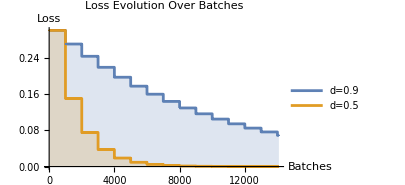

```mathematica
decaySchedule1[b_,bmax_]:=0.9^Floor[b/1000];
decaySchedule2[b_,bmax_]:=0.5^Floor[b/1000];

{result1,result2}=trainedNetwork/@{decaySchedule1,decaySchedule2};

ListPlot[
{result1,result2},
Filling->Axis,
Mesh->All,
Joined->True,
PlotLabel->"Loss Evolution Over Batches",
AxesLabel->{"Batches","Loss"},
PlotLegends->Placed[{"d=0.9","d=0.5"},{0.75,0.7}],
ImageSize->300
]
```

code6.27 Exponential Decay Schedules (NN)

(* Two different learning rate decay schedules (two exponential decay schedules) are employed during training to monitor the network’s learning progress, and the training is limited to 5 rounds with a batch size of 5000. By visualizing the training progress through the evolution of learning rates over rounds, the code assesses the impact of different learning rate schedules on the network’s ability to learn the desired mapping accurately: *)

```mathematica
trainingData=Flatten@Table[{x,y}->{Exp[-Norm[{x,y}]]},{x,-3,3,.005},{y,-3,3,.005}];

network=NetChain[
{
10,LogisticSigmoid,
5,LogisticSigmoid,
5,LogisticSigmoid,
1
},
"Input"->2
];

initializedNetwork=NetInitialize[
network,
Method->{"Random","Weights"->0.05,"Biases"->0.05},
RandomSeeding->Automatic
];

trainedNetwork[learningRateSchedule_]:=NetTrain[
initializedNetwork,
trainingData,
{"BatchLossList",
<|
"Property"->"LearningRate",
"Interval"->"Batches"
|>
},
MaxTrainingRounds->5,
LearningRate->0.3,
BatchSize->5000,
Method->{"SGD","LearningRateSchedule"->learningRateSchedule}
]
```

(* Define learning rate schedules using exponential decay: *) (* With “LearningRateSchedule”->f, the learning rate for a given batch will be calculated as initial*f[batch, total], where batch is the current batch number, total is the total number of batches that will be visited during training, and initial is the initial learning rate specified using the LearningRate option. The value returned by f should be a number between 0 and 1: *)

(* Exponential Decay: α_t=α_0 e^(-d*t), d is the decay rate parameter. Note that, we used “Interval”->”Batches” not “Interval”->”Rounds”: *)

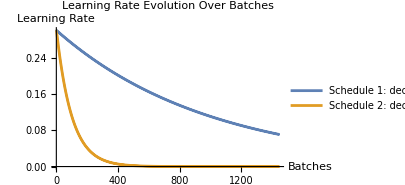

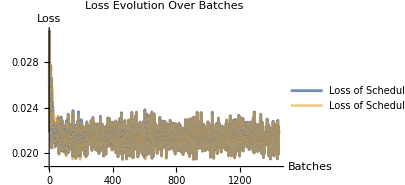

```mathematica
generateSchedule[decayRate_]:=Function[
{b,bmax},
Exp[-b*decayRate]
]

decaySchedule1=generateSchedule[0.001];
decaySchedule2=generateSchedule[0.01];

{loss1,result1,loss2,result2}=Flatten[trainedNetwork/@{decaySchedule1,decaySchedule2},1];

ListPlot[
{result1,result2},
PlotRange->Full,
Mesh->All,
Joined->True,
PlotLabel->"Learning Rate Evolution Over Batches",
PlotLegends->{"Schedule 1: decayRate=0.001","Schedule 2: decayRate=0.01"},
ImageSize->300,
AxesLabel->{"Batches","Learning Rate"}
]

ListPlot[
{loss1,loss2},
PlotRange->Full,
Mesh->All,
Joined->True,
PlotStyle->{Opacity[0.9],Opacity[0.5]},
PlotLabel->"Loss Evolution Over Batches",
PlotLegends->{"Loss of Schedule 1","Loss of Schedule 2"},
ImageSize->300,
AxesLabel->{"Batches","Loss"}
]
```

code 6.28 Polynomial Learning Rate (NN)

(* Two different learning rate decay schedules (polynomial learning rate policy) are employed during training to monitor the network’s learning progress, and the training is limited to 10 rounds with a batch size of 1024. By visualizing the training progress through the evolution of learning rates over batches, the code assesses the impact of different learning rate schedules on the network’s ability to learn the desired mapping accurately: *)

```mathematica
trainingData=Flatten@Table[{x,y}->{Exp[-Norm[{x,y}]]},{x,-3,3,.005},{y,-3,3,.005}];

network=NetChain[
{
10,LogisticSigmoid,
5,LogisticSigmoid,
5,LogisticSigmoid,
1
},
"Input"->2
];

initializedNetwork=NetInitialize[
network,
Method->{"Random","Weights"->0.05,"Biases"->0.05},
RandomSeeding->Automatic
];

trainedNetwork[learningRateSchedule_]:=NetTrain[
initializedNetwork,
trainingData,
<|
"Property"->"LearningRate",
"Interval"->"Batches"
|>,
MaxTrainingRounds->10,
LearningRate->0.3,
BatchSize->1024,
Method->{"SGD","LearningRateSchedule"->learningRateSchedule}
]
```

(* With “LearningRateSchedule”->f, the learning rate for a given batch will be calculated as (initial*f[batch, total]), where batch is the current batch number, total is the total number of batches that will be visited during training, and initial is the initial learning rate specified using the LearningRate option. The value returned by f should be a number between 0 and 1: *)

(* Polynomial Learning Rate Policy function α_ t=α _ 0*(1-t/T _t)^n, where α_0=0.3 represents the initial learning rate, t signifies the number of iterations, and T_t denotes the total number of iterations. The power term, n=0.5 or n=1.8, within the formula, serves as a critical determinant, shaping the decay characteristics of the learning rate. *)

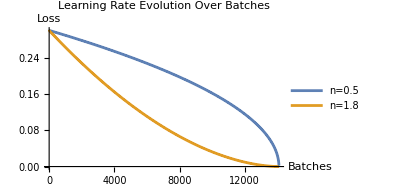

```mathematica
Clear[decaySchedule1,decaySchedule2];

decaySchedule1[b_,bmax_]:=(1-b/bmax)^0.5;
decaySchedule2[b_,bmax_]:=(1-b/bmax)^1.8;

{result1,result2}=trainedNetwork/@{decaySchedule1,decaySchedule2};

ListPlot[
{result1,result2},
Mesh->All,
Joined->True,
PlotLabel->"Learning Rate Evolution Over Batches",
AxesLabel->{"Batches","Loss"},
PlotLegends->Placed[{"n=0.5","n=1.8"},{0.75,0.7}],
ImageSize->300
]
```

code 6.29 Triangular Learning Rate (NN)

(* Two different learning rate decay schedules (two triangular learning rate schedules) are employed during training to monitor the network’s learning progress, and the training is limited to 20 rounds with a batch size of 1024. By visualizing the training progress through the evolution of learning rates over rounds, the code assesses the impact of different learning rate schedules on the network’s ability to learn the desired mapping accurately: *)

```mathematica
trainingData=Flatten@Table[{x,y}->{Exp[-Norm[{x,y}]]},{x,-3,3,.005},{y,-3,3,.005}];

network=NetChain[
{
10,LogisticSigmoid,
5,LogisticSigmoid,
5,LogisticSigmoid,
1
},
"Input"->2
];

initializedNetwork=NetInitialize[
network,
Method->{"Random","Weights"->0.05,"Biases"->0.05},
RandomSeeding->Automatic
];

trainedNetwork[learningRateSchedule_]:=NetTrain[
initializedNetwork,
trainingData,
{"RoundLossList",
<|
"Property"->"LearningRate",
"Interval"->"Batches"
|>
},
MaxTrainingRounds->20,
LearningRate->0.3,
BatchSize->1024,
Method->{"SGD","LearningRateSchedule"->learningRateSchedule}
]
```

(* With “LearningRateSchedule”->f, the learning rate for a given batch will be calculated as initial*f[batch, total], where batch is the current batch number, total is the total number of batches that will be visited during training, and initial is the initial learning rate specified using the LearningRate option. The value returned by f should be a number between 0 and 1: *)

(* Triangular learning rate schedule: α_t=α_min+(α_max-α_min)*max[0,(1-x)], where x=|t/s-2c+1|, and c can be calculated as, c=⌊1+t/2s⌋, where α_min is the specified lower (i.e., base) learning rate, t is the number of iterations of training, and α_t is the computed learning rate. s is half the period or cycle length and α_max is the maximum learning rate boundary. Note that, we used “Interval”->”Rounds” not “Interval”->”Batches”: *)

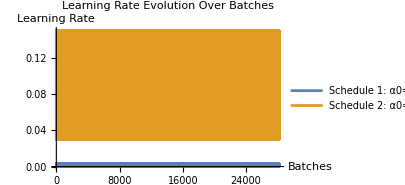

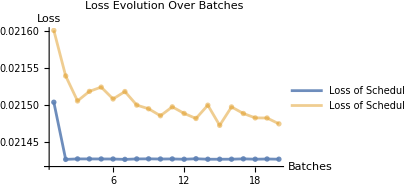

```mathematica
generateSchedule[baseLR_,maxLR_,stepsize_]:=Module[
{cycle,x},
Function[
{b,bmax},
cycle=Floor[1+b/(2*stepsize)];
x=Abs[b/stepsize-2*cycle+1];
baseLR+(maxLR-baseLR)*Max[0,(1-x)]
]
]

decaySchedule1=generateSchedule[0.001,0.01,2];
decaySchedule2=generateSchedule[0.1,0.5,5];

{loss1,result1,loss2,result2}=Flatten[trainedNetwork/@{decaySchedule1,decaySchedule2},1];

ListPlot[
{result1,result2},
PlotRange->Full,
Mesh->All,
Joined->True,
PlotLabel->"Learning Rate Evolution Over Batches",
PlotLegends->{"Schedule 1: α0=0.3,αmin=0.001,αmax=0.01,HalfCycleLength=2","Schedule 2: α0=0.3,αmin=0.1,αmax=0.5,HalfCycleLength=5"},
ImageSize->300,
AxesLabel->{"Batches","Learning Rate"}
]

ListPlot[
{loss1,loss2},
PlotRange->Full,
Mesh->All,
Joined->True,
PlotStyle->{Opacity[0.9],Opacity[0.5]},
PlotLabel->"Loss Evolution Over Batches",
PlotLegends->{"Loss of Schedule 1","Loss of Schedule 2"},
ImageSize->300,
AxesLabel->{"Batches","Loss"}
]
```

code 6.30 Adam Optimizer (NN)

(* The code aims to train a neural network using the Adam optimizer with various hyperparameter configurations, starting with generating example data representing 2D input points and their corresponding output values. The neural network architecture, consisting of linear layers and ReLU activation functions, is defined and initialized with Kaiming initialization. Through the training process, the network learns to minimize the loss function on the provided dataset, with training progress monitored and recorded. By adjusting the beta1 and beta2 parameters of the Adam optimizer, the code systematically explores different optimization settings to observe their impact on training performance. Finally, the code visualizes the evolution of loss over training rounds for each hyperparameter configuration, providing insights into how different optimization settings influence the network’s learning dynamics: *)

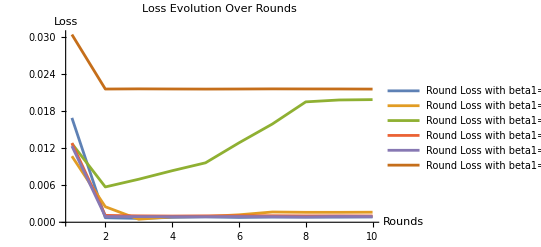

```mathematica
trainingData=Flatten@Table[{x,y}->{Exp[-Norm[{x,y}]]},{x,-3,3,.005},{y,-3,3,.005}];

network=NetChain[
{
10,ElementwiseLayer[Ramp],
10,ElementwiseLayer[Ramp],
1
},
"Input"->2
];

initializedNetwork=NetInitialize[
network,
Method->{"Kaiming","Distribution"->"Normal"},
RandomSeeding->Automatic
];

trainedNetwork[method_,beta1_,beta2_]:=NetTrain[
initializedNetwork,
trainingData,
"RoundLossList",
MaxTrainingRounds->10,
LearningRate->0.1,
BatchSize->1024,
Method->{method,"Beta1"->beta1,"Beta2"->beta2,"Epsilon"->0.00001}
];

roundLoss1=trainedNetwork["ADAM",0.9,0.999];
roundLoss2=trainedNetwork["ADAM",0.7,0.999];
roundLoss3=trainedNetwork["ADAM",0.5,0.999];

roundLoss4=trainedNetwork["ADAM",0.9,0.95];
roundLoss5=trainedNetwork["ADAM",0.9,0.90];
roundLoss6=trainedNetwork["ADAM",0.9,0.80];

ListPlot[
{roundLoss1,roundLoss2,roundLoss3,roundLoss4,roundLoss5,roundLoss6},
PlotLegends->{
"Round Loss with beta1=0.9,beta2=0.999",
"Round Loss with beta1=0.7,beta2=0.999",
"Round Loss with beta1=0.5,beta2=0.999",
"Round Loss with beta1=0.95,beta2=0.9",
"Round Loss with beta1=0.90,beta2=0.9",
"Round Loss with beta1=0.80,beta2=0.9"
},
Joined->True,
PlotRange->Full,
PlotLabel->"Loss Evolution Over Rounds",
AxesLabel->{"Rounds","Loss"}
]
```

code 6.31 RMSProp Optimizer (NN)

(* The code aims to train a neural network using the RMSProp optimizer with various hyperparameter configurations, starting with generating example data representing 2D input points and their corresponding output values. The neural network architecture, consisting of linear layers and ReLU activation functions, is defined and initialized with Kaiming initialization. Through the training process, the network learns to minimize the loss function on the provided dataset, with training progress monitored and recorded. By adjusting the beta and momentum parameters of the RMSProp optimizer, the code systematically explores different optimization settings to observe their impact on training performance. Finally, the code visualizes the evolution of loss over training rounds for each hyperparameter configuration, providing insights into how different optimization settings influence the network’s learning dynamics: *)

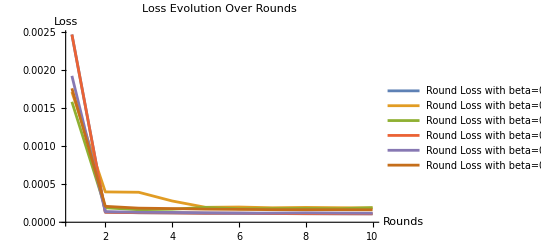

```mathematica
trainingData=Flatten@Table[{x,y}->{Exp[-Norm[{x,y}]]},{x,-3,3,.005},{y,-3,3,.005}];

network=NetChain[
{
10,ElementwiseLayer[Ramp],
10,ElementwiseLayer[Ramp],
1
},
"Input"->2
];

initializedNetwork=NetInitialize[
network,
Method->{"Kaiming","Distribution"->"Normal"},
RandomSeeding->Automatic
];

trainedNetwork[method_,beta_,momentum_]:=NetTrain[
initializedNetwork,
trainingData,
"RoundLossList",
MaxTrainingRounds->10,
LearningRate->0.01,
BatchSize->1024,
Method->{method,"Beta"->beta,"Momentum"->momentum,"Epsilon"->0.000001}
];

roundLoss1=trainedNetwork["RMSProp",0.95,0.9];
roundLoss2=trainedNetwork["RMSProp",0.80,0.9];
roundLoss3=trainedNetwork["RMSProp",0.70,0.9];

roundLoss4=trainedNetwork["RMSProp",0.95,0.9];
roundLoss5=trainedNetwork["RMSProp",0.95,0.8];
roundLoss6=trainedNetwork["RMSProp",0.95,0.7];

ListPlot[
{roundLoss1,roundLoss2,roundLoss3,roundLoss4,roundLoss5,roundLoss6},
PlotLegends->{
"Round Loss with beta=0.95, momentum=0.9",
"Round Loss with beta=0.80, momentum=0.9",
"Round Loss with beta=0.70, momentum=0.9",
"Round Loss with beta=0.90, momentum=0.95",
"Round Loss with beta=0.80, momentum=0.95",
"Round Loss with beta=0.70, momentum=0.95"
},
Joined->True,
PlotRange->Full,
PlotLabel->"Loss Evolution Over Rounds",
AxesLabel->{"Rounds","Loss"}
]
```

code 6.32 ADAM, RMSProp, SGD, with step decay and triangular schedule (NN)

(* The code aims to train a neural network on generated example data by comparing the performance of different optimization methods and learning rate schedules. It first generates training data based on a predefined function and defines a neural network architecture. The network is then initialized with appropriate weights using Kaiming initialization. The code proceeds to train the network using various optimization methods (ADAM, RMSProp, SGD) and learning rate schedules (step decay, triangular schedule) while monitoring training progress by tracking loss function evolution and learning rate changes. The goal is to visualize and analyze how different optimization strategies impact the training process, facilitating the identification of the most effective approach for the given dataset and network architecture: *)

```mathematica
trainingData=Flatten@Table[{x,y}->{Exp[-Norm[{x,y}]]},{x,-3,3,.005},{y,-3,3,.005}];

network=NetChain[
{
10,ElementwiseLayer[Ramp],
10,ElementwiseLayer[Ramp],
1
},
"Input"->2
];

initializedNetwork=NetInitialize[
network,
Method->{"Kaiming","Distribution"->"Normal"}
];

trainedNetwork[method_,learningRateSchedule_]:=NetTrain[
initializedNetwork,
trainingData,
{"RoundLossList",
<|
"Property"->"LearningRate",
"Interval"->"Batches"
|>
},
MaxTrainingRounds->5,
LearningRate->0.1,
BatchSize->1024,
Method->{method,"LearningRateSchedule"->learningRateSchedule}
];
```

(* With “LearningRateSchedule”->f, the learning rate for a given batch will be calculated as initial*f[batch, total], where batch is the current batch number, total is the total number of batches that will be visited during training, and initial is the initial learning rate specified using the LearningRate option. The value returned by f should be a number between 0 and 1: *)

(* Step decay: αt =α0 ∗d⌊t/s⌋, α_0=0.3 is the initial learning rate, d=0.9 is the constant factor (drop factor or decay factor) by which the learning rate drops each time,s=1000 is the step size, indicating after how many iterations the learning rate should be decayed.*)

```mathematica
Clear[decaySchedule1];
decaySchedule1[b_,bmax_]:=0.9^Floor[b/1000];
```

(* Triangular learning rate schedule: α_t=α_min+(α_max-α_min)*max[0,(1-x)], where x=|t/s-2c+1|, and c can be calculated as, c=⌊1+t/2s⌋, where α_min is the specified lower (i.e., base) learning rate, t is the number of iterations of training, and α_t is the computed learning rate. s is half the period or cycle length and α_max is the maximum learning rate boundary. Note that, we used “Interval”->”Batches” not “Interval”->”Rounds”: *

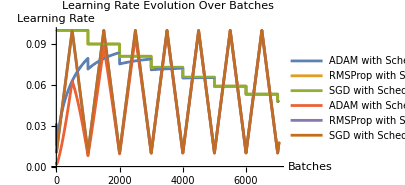

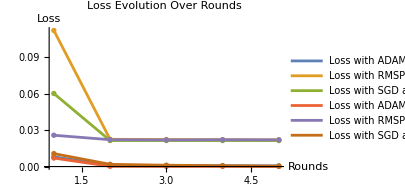

```mathematica
generateSchedule[baseLR_,maxLR_,stepsize_]:=Module[
{cycle,x},
Function[
{b,bmax},
cycle=Floor[1+b/(2*stepsize)];
x=Abs[b/stepsize-2*cycle+1];
baseLR+(maxLR-baseLR)*Max[0,(1-x)]
]
]

decaySchedule2=generateSchedule[0.1,1,500];

{loss1,result1,loss2,result2,loss3,result3,loss4,result4,loss5,result5,loss6,result6}=Flatten[
trainedNetwork@@@{
{"ADAM",decaySchedule1},
{"RMSProp",decaySchedule1},
{"SGD",decaySchedule1},
{"ADAM",decaySchedule2},
{"RMSProp",decaySchedule2},
{"SGD",decaySchedule2}
},1];

ListPlot[{result1,result2,result3,result4,result5,result6},PlotRange->Full,Mesh->All,Joined->True,PlotLabel->"Learning Rate Evolution Over Batches",PlotLegends->{"ADAM with Schedule 1","RMSProp with Schedule 1","SGD with Schedule 1","ADAM with Schedule 2","RMSProp with Schedule 2","SGD with Schedule 2"},ImageSize->300,AxesLabel->{"Batches","Learning Rate"}] ListPlot[{loss1,loss2,loss3,loss4,loss5,loss6},PlotRange->Full,Mesh->All,Joined->True,PlotLabel->"Loss Evolution Over Rounds",PlotLegends->{"Loss with ADAM and Schedule 1","Loss with RMSProp and Schedule 1","Loss with SGD and Schedule 1","Loss with ADAM and Schedule 2","Loss with RMSProp and Schedule 2","Loss with SGD and Schedule 2"},ImageSize->300,AxesLabel->{"Rounds","Loss"}]
```